# DTQW Optimizada (Wang et al.)

## Modelo de caminata cuántica

Implementación de caminata cuántica discreta en el tiempo basada en el modelo presentado por Wang et al. en [1]. Dónde la caminata está dada por

-Graphics-

dónde

-Graphics-

## Definiciones

### Contenido externo

```mathematica
MatrixPartialTrace=ResourceFunction["MatrixPartialTrace"];
```

### Constantes

```mathematica
α=π/6.
```

0.523599

### Operadores optimizados

```mathematica
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
```

```mathematica
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
```

```mathematica
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
```

```mathematica
FuzzyOperator[n_]:=RotateLeft[IdentityMatrix[n,SparseArray]]
```

```mathematica
DTQW[rho_,n_]:=Module[{ρ},
ρ=rho;
Do[ρ=Chop[#.ArrayPad[ρ,{{0,2},{0,2}}].ConjugateTranspose[#]]&[UnitaryOperator[t+1]],{t,n}];
ρ
]
```

```mathematica
FuzzyDTQW[rho_,n_,p_]:=Module[{ρ,pre},
ρ=rho;
Do[
pre=(#.ArrayPad[ρ,{{0,2},{0,2}}].ConjugateTranspose[#])&[UnitaryOperator[t+1]];
ρ=Chop[(1-p)*pre+p*#.pre.ConjugateTranspose[#]]&[RotateLeft[IdentityMatrix[2*t+2,SparseArray],2]],
{t,n}
];
ρ
]
```

### Una caminata

```mathematica
rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
AbsoluteTiming[rho=DTQW[rho,150];]
```

{2.71099,Null}

```mathematica
probs=Diagonal@MatrixPartialTrace[rho,2,{151,2}];
```

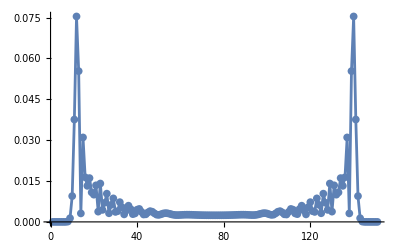

```mathematica
ListLinePlot[probs,
PlotRange->All,
Mesh->All
]
```

### Fuzzy walk

```mathematica
rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
```

```mathematica
AbsoluteTiming[rho=FuzzyDTQW[rho,150,0.7];]
```

{2.6358,Null}

```mathematica
probs2=Diagonal@MatrixPartialTrace[rho,2,{151,2}];
```

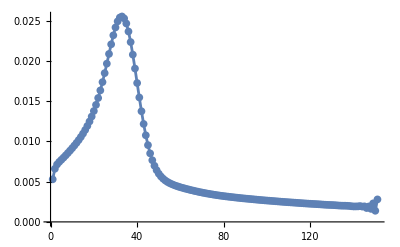

```mathematica
ListLinePlot[probs2,
PlotRange->All,
Mesh->All
]
```

### Una caminata con fuzzy al final

#### Caminata

```mathematica
rho=Outer[Times,#,Conjugate[#]]&[{1,ⅈ}/Sqrt[2.]];
AbsoluteTiming[rho=DTQW[rho,150];]
```

{2.74512,Null}

```mathematica
probs3=Diagonal@(#.MatrixPartialTrace[rho,2,{151,2}].ConjugateTranspose[#])&[FuzzyOperator[151]];
```

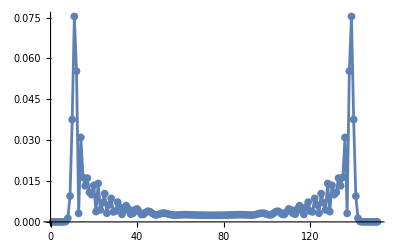

```mathematica
ListLinePlot[probs3,
PlotRange->All,
Mesh->All
]
```

#### Comparaciones

```mathematica
Total/@{probs,probs3}
```

{1.,1.+0. ⅈ}

```mathematica
Chop[probs]==Chop[probs3]
```

False

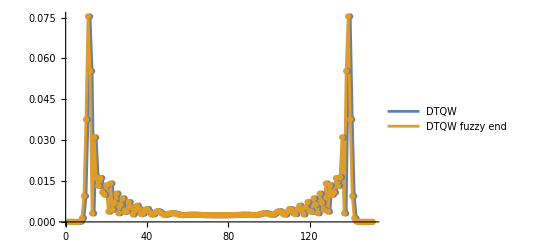

```mathematica
ListLinePlot[{probs,probs3},
PlotRange->All,
Mesh->All,
PlotLegends->{"DTQW","DTQW fuzzy end"}
]
```

```mathematica
RotateLeft[Chop[probs]]==Chop[probs3]
```

True

## Extras

```mathematica
f[x_?MatrixQ]:="hola"
```

```mathematica
f[{{a,b},{c,d}}]
```

hola

```mathematica
ss=Ket[{1,0}]
```

1,0

```mathematica
vs=Ket[{a,b}]/5+Ket[{c,d}]+2Ket[{e,f}]
```

(a,b)/5+c,d+2 e,f

```mathematica
dm=Ket[{a,b}].Bra[{z,y}]+3Ket[{c,d}].Bra[{x,w}]/2+Ket[{e,f}].Bra[{v,u}]
```

a,b.z,y+3/2 c,d.x,w+e,f.v,u

```mathematica
Cases[#,_Ket,Infinity]&/@{ss,vs,dm}//Column
```

{}
{a,b,c,d,e,f}
{a,b,c,d,e,f}

## Referencias

[1] Q.-Q. Wang et al., “Efficient learning of mixed-state tomography for photonic quantum walk”, Sci. Adv., vol. 10, núm. 11, p. eadl4871, mar. 2024, doi: 10.1126/sciadv.adl4871.